```mathematica
(* Analysis of population diversity *)
```

```mathematica
(* Bounding function: used to bound the variance of the elements generated within the bounds;  bound=0.6 has been chosen to limit to 1/4 the variance of a random population generated in [0,1] - according to Popoviciu's inequality of variances of bounded probability distributions *)
```

```mathematica
bound=0.6; B[u_]:=If[u≤bound,u,bound]
```

```mathematica
(* Scaling coefficient in the linear function describing the relationship between the variance of the population obtained after mutation and correction and the variance of the current population (pm=mutation probability, pv=violation probability, F=scale factor, m=population size) *)
```

```mathematica
c[pm_,pv_,m_,F_]:=(1-pm)^2+pm*pv*(1-pm)*(m-1)/m+pm^2*(1-pv)^2*B[(m-1)/m+2*F^2]+2*pm*(1-pm)*B[(m-1)/m+F^2]+
2pm^2*pv*(1-pv)*B[(m-1)^2/(2*m^2)+(m-1)/m*F^2]
```

```mathematica
(* Free term in the linear function describing the relationship between the variance of the population obtained after mutation and correction and the variance of the current population (pm=mutation probability, pv=violation probability, F=scale factor, m=population size, Xbar = mean of the current population, Rmean=mean of the corrected elements, Rvar=variance of the corrected elements)*)
```

```mathematica
d[pm_,pv_,m_,F_,Xbar_,Rmean_,Rvar_]:=pm*pv*(1-pm*pv)*(m-1)/m*(Xbar-Rmean)^2+pm*pv*(1-(1-pm*pv)/m)*Rvar
```

```mathematica
(* computation of the mutation probability, depending on the crossover type (CR = crossover rate, n=problem size *)
```

```mathematica
pmBin[CR_,n_]:=CR*(1-1/n)+1/n;  pmExp[CR_,n_]:=(1-CR^n)/(n*(1-CR))
```

```mathematica
(* computation of the variance over generations *)
```

```mathematica
(* Assumption: constant violation probability (pv=F/3) *)
```

```mathematica
lvar[pm_,pv_,m_,F_,Xbar_,Rmean_,Rvar_,varInit_,gen_]:=Module[{var={varInit}},Do[var=Append[var,c[pm,pv,m,F]*Last[var]+d[pm,pv,m,F,Xbar,Rmean,Rvar]],{gen}]; Return[var]]
```

```mathematica
(* Particular case:  saturate;  the violation probability changes in time: pv(g+1)=pv(g)/2+(1-pv(g))(pv(g)^2F/4+(1-pv(g)^2)F/3) *)
```

```mathematica
lvarSaturate[pm_,pv_,m_,F_,Xbar_,Rmean_,Rvar_,varInit_,gen_]:=Module[{var={varInit},Fsat={F/3}},Do[Fsat=Append[Fsat,Last[Fsat]/2+(1-Last[Fsat])*(Last[Fsat]^2*F/4+(1-Last[Fsat]^2)*F/3)];var=Append[var,c[pm,Last[Fsat],m,F]*Last[var]+d[pm,Last[Fsat],m,F,Xbar,Rmean,Rvar]],{gen}]; Return[var]]
```

```mathematica
(* list of values for F and CR *)
```

```mathematica
listF={0.05,0.285,0.52,0.755,0.99}; listCR={0.05,0.285,0.52,0.755,0.99};
```

```mathematica
(* Computation of the standard deviation over generations for uniform resampling, saturate and mirror. Assumptions: n=30, m=100, 100 generations, binomial crossover *)
```

```mathematica
n=30; m=100; gen = 100;
```

```mathematica
(* Uniform resampling:  Rmean=Xbar=1/2, Rvar=1/12 *)
```

```mathematica
Xbar=0.5; Rmean=0.5; Rvar=1.0/12; varinit=1.0/12;stdevUnif=Table[Sqrt[lvar[pmBin[listCR[[indCR]],n],listF[[indF]]/3,m,listF[[indF]],Xbar,Rmean,Rvar,varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* Saturate: Rmean=Xbar=1/2, Rvar=1/4 *)
```

```mathematica
Xbar=0.5; Rmean=0.5; Rvar=1.0/4; varinit=1.0/12;
stdevSaturate=Table[Sqrt[lvarSaturate[pmBin[listCR[[indCR]],n],listF[[indF]]/3,m,listF[[indF]],Xbar,Rmean,Rvar,varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* Mirror: Rmean=Xbar=1/2, Rvar = F^2/10-F/4+1/4 *)
```

```mathematica
Xbar=0.5; Rmean=0.5;RvarMirror[F_]:=F^2/10-F/4+1/4 ; varinit=1.0/12;stdevMirror=Table[Sqrt[lvar[pmBin[listCR[[indCR]],n],listF[[indF]]/3,m,listF[[indF]],Xbar,Rmean,RvarMirror[listF[[indF]]],varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* color codes *)
```

```mathematica
colors={{0.4,0.7607843137254902,0.6470588235294118},{0.9882352941176471,0.5529411764705883,0.3843137254901961},{0.5529411764705883,0.6274509803921569,0.796078431372549},{0.9058823529411765,0.5411764705882353,0.7647058823529411},{0.6509803921568628,0.8470588235294118,0.32941176470588235},{0.8980392156862745,0.7686274509803922,0.5803921568627451}};
```

```mathematica
gFCR=Table[Which[indCR==1&&indF==1,ListLinePlot[{stdevUnif[[indF,indCR]],stdevMirror[[indF,indCR]],stdevSaturate[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[1]]],RGBColor[colors[[2]]],RGBColor[colors[[3]]]},PlotRange->{{0,gen},{0,0.5}},PlotLegends->Placed[{Text[Style["unif",FontSize->10]],Text[Style["mirror",FontSize->10]],Text[Style["saturate",FontSize->10]]},{Right,Top}],Frame->True, FrameLabel->{StringJoin["CR=",ToString[listCR[[indCR]]]],StringJoin["F=",ToString[listF[[indF]]]]}],indCR==1&& indF≠1,ListLinePlot[{stdevUnif[[indF,indCR]],stdevMirror[[indF,indCR]],stdevSaturate[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[1]]],RGBColor[colors[[2]]],RGBColor[colors[[3]]]},PlotRange->{{0,gen},{0,0.5}},Frame->True, FrameLabel->{"",StringJoin["F=",ToString[listCR[[indF]]]]}], indCR≠1&& indF==1,ListLinePlot[{stdevUnif[[indF,indCR]],stdevMirror[[indF,indCR]],stdevSaturate[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[1]]],RGBColor[colors[[2]]],RGBColor[colors[[3]]]},PlotRange->{{0,gen},{0,0.5}},Frame->True, FrameLabel->{StringJoin["CR=",ToString[listCR[[indCR]]]],""}],indCR≠1 && indF≠ 1,ListLinePlot[{stdevUnif[[indF,indCR]],stdevMirror[[indF,indCR]],stdevSaturate[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[1]]],RGBColor[colors[[2]]],RGBColor[colors[[3]]]},PlotRange->{{0,gen},{0,0.5}},Frame->True, FrameLabel->{"",""}]],{indF,Length[listF],1,-1},{indCR,1,Length[listCR]}];
```

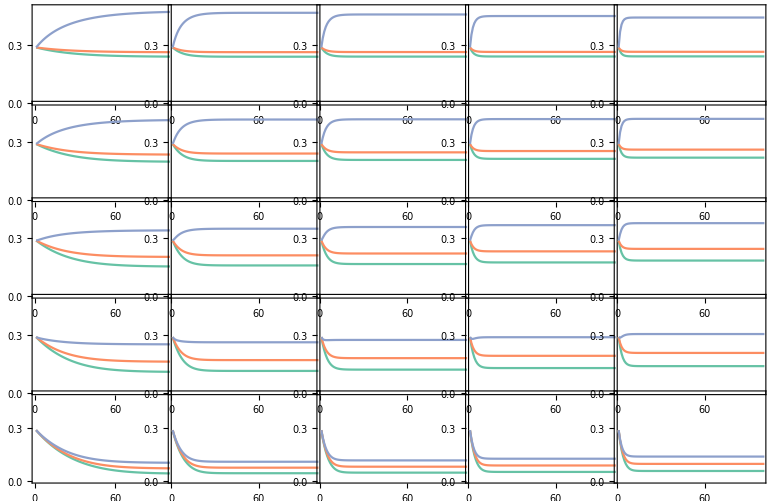

```mathematica
GraphicsGrid[gFCR,Spacings->{Scaled[-0.2],Scaled[-0.2]}]
```